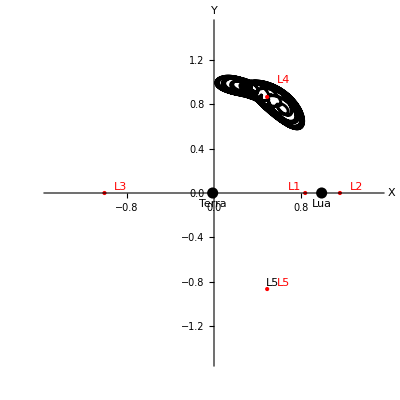

```mathematica
ClearAll[mu,eqns,sol,rotatingFrameDynamics,x,y,r1,L1,L2,L3,L4,L5,m1,m2]


mu=0.01215;

L1={FindRoot[x-(1-mu)/(x+mu)^2+mu/(x-(1-mu))^2==0,{x,0.5}]//Values//First,0};
L2={FindRoot[x-(1-mu)/(x+mu)^2-mu/(x-(1-mu))^2==0,{x,1.5}]//Values//First,0};
L3={FindRoot[x+(1-mu)/(x+mu)^2+mu/(x-(1-mu))^2==0,{x,-1}]//Values//First,0};
L4={1/2-mu,Sqrt[3]/2};
L5={1/2-mu,-Sqrt[3]/2};

rotatingFrameDynamics[t_,{x_,y_,vx_,vy_}]:=Module[{r1,r2,ax,ay},r1=Sqrt[(x+mu)^2+y^2];
r2=Sqrt[(x-(1-mu))^2+y^2];
ax=2 vy+x-(1-mu) (x+mu)/r1^3-mu (x-(1-mu))/r2^3;
ay=-2 vx+y-(1-mu) y/r1^3-mu y/r2^3;
{vx,vy,ax,ay}];


sol=NDSolve[{Derivative[1][x][t]==vx[t],Derivative[1][y][t]==vy[t],Derivative[1][vx][t]==2 vy[t]+x[t]-(1-mu) (x[t]+mu)/((x[t]+mu)^2+y[t]^2)^(3/2)-mu (x[t]-(1-mu))/((x[t]-(1-mu))^2+y[t]^2)^(3/2),Derivative[1][vy][t]==-2 vx[t]+y[t]-(1-mu) y[t]/((x[t]+mu)^2+y[t]^2)^(3/2)-mu y[t]/((x[t]-(1-mu))^2+y[t]^2)^(3/2),x[0]==L4[[1]]+0.0075,y[0]==L4[[2]]+0.0075,vx[0]==0,vy[0]==0},{x,y,vx,vy},{t,0,3000}];


trajectory=ParametricPlot[Evaluate[{{x[t],y[t]}/. sol}],{t,0,300},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{"X","Y"},PlotStyle->{Normal,Black}];

pontos=Graphics[{Red,PointSize[Large],Point[L1],Point[L2],Point[L3],Point[L4],Point[L5],Text["L1",L1+{-0.10,0.05}],Text["L2",L2+{0.15,0.05}],Text["L3",L3+{0.15,0.05}],Text["L4",L4+{0.15,0.15}],Text["L5",L5+{0.15,0.05}],Black,PointSize[0.02],Point[{-mu,0}],Point[{1-mu,0}],Text["Lua",{1-mu,-0.10}],Text["Terra",{-mu,-0.10}]}];

Show[trajectory,pontos,Graphics[{Text["L4",L4+{0.05,0.05}],Text["L5",L5+{0.05,0.05}]}],PlotRange->{{-1.5,1.5},{-1.5,1.5}},Axes->True]

Manipulate[Module[{currentTrajectory},currentTrajectory=ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,tmax},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{"X","Y"},PlotStyle->{Normal,Black}];
Show[currentTrajectory,pontos,Graphics[],PlotRange->{{-1.5,1.5},{-1.5,1.5}},Axes->False]],{{tmax,10,"Time"},1,200,1}]
```